# Renormalized Self energies of W/Z and δρ

```mathematica
Quit[];
```

```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts= True;
<<FeynCalc`
$FAVerbose=0;
```

## Create the 1 loop topologies needed in Unitary gauge

```mathematica
$ExcludeTopologies[V4onExt]=FreeQ[Cases[#,Propagator[External][__]],Vertex[4]]&;
```

```mathematica
t11 = CreateTopologies[1,1->1, ExcludeTopologies->{Tadpoles,V4onExt}]; 
ct11 = CreateCTTopologies[1,1->1,ExcludeTopologies->{Tadpoles,V4onExt}];
```

## Create diagrams, include only those that contain W/Z and Higgs

```mathematica
diagWselfE = InsertFields[t11, V[3]->{V[3]},InsertionLevel->{Classes},ExcludeParticles->{F},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz},LastSelections->{S[1]}]; 
diagWselfEct = InsertFields[ct11, V[3]->{V[3]},InsertionLevel->{Classes}, Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
diagZselfE = InsertFields[t11, V[2]->{V[2]},InsertionLevel->{Classes}, ExcludeParticles->{F},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz},LastSelections->{S[1]}]; 
diagZselfEct = InsertFields[ct11, V[2]->{V[2]},InsertionLevel->{Classes}, Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
```

```mathematica
Paint[diagWselfE,ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{200,200}];
```

```mathematica
Paint[diagZselfE,ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{200,200}]
```

## Calculate 1 loop amplitudes and counter-term amplitudes

```mathematica
GaugeXi[Z]
```

ξ_Z

```mathematica
(*Calculate unrenormalized Higgs contribution to WW and ZZ self energy at 1 loop*)
GaugeXi
ampWselfE=FCFAConvert[CreateFeynAmp[diagWselfE,Truncated->True],IncomingMomenta->{q},OutgoingMomenta->{q},LorentzIndexNames-> {μ,ν}, LoopMomenta->{l},List->False,ChangeDimension->D,DropSumOver->True,SMP->True,UndoChiralSplittings->True]//Contract//FCTraceFactor;
ampZselfE=FCFAConvert[CreateFeynAmp[diagZselfE,Truncated->True],IncomingMomenta->{q},OutgoingMomenta->{q},LorentzIndexNames-> {μ,ν}, LoopMomenta->{l},List->False,ChangeDimension->D,DropSumOver->True,SMP->True,UndoChiralSplittings->True]//Contract//FCTraceFactor;
ampWselfEct=FCFAConvert[CreateFeynAmp[diagWselfEct,Truncated->True],IncomingMomenta->{q},OutgoingMomenta->{q},LorentzIndexNames-> {μ,ν}, LoopMomenta->{l},List->False,ChangeDimension->D,DropSumOver->True,SMP->True,UndoChiralSplittings->True]//Contract//FCTraceFactor;
ampZselfEct=FCFAConvert[CreateFeynAmp[diagZselfEct,Truncated->True],IncomingMomenta->{q},OutgoingMomenta->{q},LorentzIndexNames-> {μ,ν}, LoopMomenta->{l},List->False,ChangeDimension->D,DropSumOver->True,SMP->True,UndoChiralSplittings->True]//Contract//FCTraceFactor;
```

## Use Parsimmino-Veltman reduction to write 1 loop amplitudes in terms of scalar integrals

```mathematica
ReducedWSelfE = TID[ampWselfE,l,ToPaVe->True];
ReducedZSelfE = TID[ampZselfE,l,ToPaVe->True];
```

```mathematica
TProj = 1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] - 1/FCI[SPD[q,q]] Pair[LorentzIndex[μ,D],Momentum[q,D]]Pair[LorentzIndex[ν,D],Momentum[q,D]]);
LProj = (Pair[LorentzIndex[μ,D],Momentum[q,D]]Pair[LorentzIndex[ν,D],Momentum[q,D]])/FCI[SPD[q,q]];
```

```mathematica
ZSelfET = Simplify[Contract[Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]/D,ReducedZSelfE]];
WSelfET = Simplify[Contract[Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]/D,ReducedWSelfE]];
```

```mathematica
SPD[q,q]=0;
```

```mathematica
ZSelfET = ZSelfET/.SMP["m_W"]->SMP["cos_W"]SMP["m_Z"];
```

```mathematica
WEh1 =  Cos[α]^2 WSelfET/.SMP["m_H"]->Subscript[m, h1];
WEh2 =  Sin[α]^2 WSelfET/.SMP["m_H"]->Subscript[m, h2];
ZEh1 = Cos[α]^2 ZSelfET/.SMP["m_H"]->Subscript[m, h1];
ZEh2 = Sin[α]^2 ZSelfET/.SMP["m_H"]->Subscript[m, h2];
Ztotal =  ZEh1 + ZEh2;
Wtotal = WEh1 + WEh2;
```

```mathematica
ZEsing = Ztotal - (Ztotal/.Sin[α]->0/.Cos[α]->1);
WEsing = Wtotal - (Wtotal/.Sin[α]->0/.Cos[α]->1);
```

```mathematica
rhoSing = Simplify[ZEsing/SMP["m_Z"]^2 - WEsing/SMP["m_W"]^2 ,Assumptions->{SMP["m_Z"]>0,SMP["m_W"]>0,Subscript[m, h1]>0, Subscript[m, h2]>0,α>0,ScaleMu>0}] ;
```

```mathematica
rhoSing;
```

```mathematica
tmp2 = Simplify[%//TrigExpand];
```

```mathematica
finalanswer =FullSimplify[tmp2//Expand,Assumptions->{SMP["m_Z"]>0,SMP["m_W"]>0,Subscript[m, h1]>0, Subscript[m, h2]>0, α>0,ScaleMu>0}];
```

```mathematica
finalanswer = finalanswer/.SMP["e"]->SMP["g_W"]*SMP["sin_W"];
```

```mathematica
finalanswer = finalanswer/.SMP["g_W"]-> Sqrt[8*SMP["G_F"]/Sqrt[2](SMP["m_W"])^2];
```

```mathematica
finalanswer = Simplify[PaXEvaluate[finalanswer,l]//FCHideEpsilon,Assumptions->{SMP["m_Z"]>0,SMP["m_W"]>0,Subscript[m, h1]>0, Subscript[m, h2]>0, α>0,ScaleMu>0}];
```

```mathematica
finalanswer = finalanswer/.Subscript[m, h1]->mh1/.Subscript[m, h2]->mh2/.SMP["m_W"]->mw/.SMP["m_Z"]->mz/.Sin[α]->sina/.SMP["G_F"]->Gf;
```

```mathematica
finalanswer - papersol ===0
```

```mathematica
numerics = finalanswer/.mw->80.385/.mz-> 91.1876/.Gf-> 1.1663787*10^-5/.mh1-> 125.7/.SMP["cos_W"]->80.385/91.1876//Simplify;
```

```mathematica
numerical[m2_,sinalpha_] := numerics/.mh2-> m2/.sina->sinalpha
```

```mathematica
numerical[m2,sina];
```

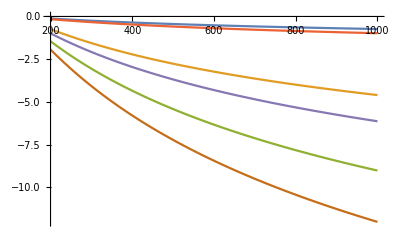

```mathematica
Plot[{10^4 sol[m2,.2],10^4 sol[m2,.5],10^4 sol[m2,.7],-10^4 numerical[m2,.2],-10^4 numerical[m2,.5],-10^4 numerical[m2,.7]},{m2,200,1000}]
```

### Here is the solution from the Singlet Extension paper Lopez et al.

```mathematica
papersol= Gf*sina^2/(2*Sqrt[2]*π^2)*(mz^2(Log[mh1^2/mh2^2] + mz^2/(mh1^2-mz^2)Log[mh1^2/mz^2] - mz^2/(mh2^2 - mz^2)Log[mh2^2/mz^2] + mh2^2/(4(mh2^2 - mz^2))Log[mh2^2/mz^2] - mh1^2/(4(mh1^2 - mz^2))Log[mh1^2/mz^2]) - mw^2(Log[mh1^2/mh2^2] + mw^2/(mh1^2-mw^2)Log[mh1^2/mw^2] - mw^2/(mh2^2 - mw^2)Log[mh2^2/mw^2] + mh2^2/(4(mh2^2 - mw^2))Log[mh2^2/mw^2] - mh1^2/(4(mh1^2 - mw^2))Log[mh1^2/mw^2]))//Simplify;
```

```mathematica
sol[m2_,sin_] := papersol/.mh2->m2/.sina->sin/.mw->80.385/.mz-> 91.1876/.Gf-> 1.1663787*10^-5/.cw-> 80.385/91.1876/.mh1-> 125.7;
```

### Okay now let’s do this calculation by hand

```mathematica
Δ = Subscript[M, H]^2 x + (1-x)Subscript[M, V]^2;
```

```mathematica
loop1 = Simplify[Normal[Integrate[C - Log[Δ/mu],{x,0,1}]],Assumptions->{Subscript[M, H]>0, Subscript[M, V]>0,C>0,mu>0}];
```

```mathematica
loop2 = Simplify[Normal[Integrate[Δ/2(C +1-Log[Δ/mu]),{x,0,1}]],Assumptions->{Subscript[M, H]>0, Subscript[M, V]>0,C>0,mu>0}];
```

```mathematica
loop[Mv_,C_]:= C^2/(16 π^2)(loop1 - loop2/Mv^2)/.Subscript[M, V]-> Mv/.mu->4Pi*μ^2
```

```mathematica
loop[Mv,C];
```

```mathematica
ΣWW = loop[Subscript[M, W],ⅈ*e*Subscript[M, W]/Sin[Subscript[θ, W]]];
ΣZZ = loop[Subscript[M, Z],ⅈ*e*Subscript[M, Z]/(Sin[Subscript[θ, W]]Cos[Subscript[θ, W]])];
```

```mathematica
ΣWWh1 = Cos[α]^2 ΣWW/.Subscript[M, H]->Subscript[M, H1];
ΣWWh2 =Sin[α]^2 ΣWW/.Subscript[M, H]->Subscript[M, H2];
ΣZZh1 = Cos[α]^2 ΣZZ/.Subscript[M, H]->Subscript[M, H1];
ΣZZh2 = Sin[α]^2 ΣZZ/.Subscript[M, H]->Subscript[M, H2];
```

```mathematica
ΣWWsing = ΣWWh1 + ΣWWh2 - (ΣWWh1/Cos[α]^2);
ΣZZsing = ΣZZh1 + ΣZZh2 - (ΣZZh1/Cos[α]^2);
```

```mathematica
rhosing = -(ΣZZsing*Cos[Subscript[θ, W]]^2)/Subscript[M, W]^2 + ΣWWsing/Subscript[M, W]^2;
```

```mathematica
rhosing = rhosing//Expand;
```

```mathematica
rhosing = Simplify[rhosing,Assumptions->{Subscript[M, H1]>0,Subscript[M, H2]>0, Subscript[M, Z]>0,Subscript[M, W]>0,C>0,μ>0}];
```

```mathematica
answer = FullSimplify[rhosing,Assumptions->{Subscript[M, H1]>0,Subscript[M, H2]>0, Subscript[M, Z]>0,Subscript[M, W]>0,C>0,μ>0}];
```

```mathematica
Coefficient[answer,C]
```

0

```mathematica
answer = answer/.C->0/.μ-> (1/(4π))^(1/2);
```

```mathematica
answer = answer/.e->SMP["g_W"]*Sin[Subscript[θ, W]];
```

```mathematica
answer = answer/.SMP["g_W"]-> Sqrt[8*SMP["G_F"]/Sqrt[2] Subscript[M, W]^2];
```

```mathematica
answer = answer/.SMP["G_F"]-> Gf;
```

```mathematica
numerics2 = answer/.Subscript[M, W]->80.385/.Subscript[M, Z]-> 91.1876/.Gf-> 1.1663787*10^-5/.Subscript[M, H1]-> 125.7/.SMP["cos_W"]->80.385/91.1876//Simplify;
```

```mathematica
numerical2[m2_,sinalpha_] := numerics2/.Subscript[M, H2]-> m2/.Sin[α]->sinalpha
```

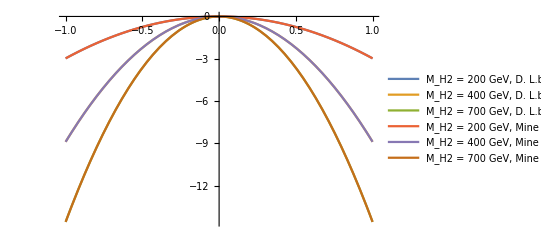

```mathematica
Plot[{10^4 sol[200,sina],10^4 sol[400,sina],10^4 sol[700,sina],10^4 numerical2[200,sina],10^4 numerical2[400,sina],10^4 numerical2[700,sina]},{sina,-1,1},PlotLegends->{"M_H2 = 200 GeV, D. L.b4opez-Val","M_H2 = 400 GeV, D. L.b4opez-Val","M_H2 = 700 GeV, D. L.b4opez-Val","M_H2 = 200 GeV, Mine","M_H2 = 400 GeV, Mine","M_H2 = 700 GeV, Mine"}]
```

### Okay so we get the correct numerical value but we are off by a sign. Feyncalc for some reason is doing unitary gauge incorrectly also which is extremely frustrating....

```mathematica
rhocont =Simplify[ (ΣWW - ΣZZ*Cos[Subscript[θ, W]]^2)/Subscript[M, W]^2/.e->SMP["g_W"]*Sin[Subscript[θ, W]]/.SMP["g_W"]-> Sqrt[8*Gf/Sqrt[2] Subscript[M, W]^2]//Expand,Assumptions->{Subscript[M, H1]>0,Subscript[M, H2]>0, Subscript[M, Z]>0,Subscript[M, W]>0,C>0,μ>0}]/.Subscript[M, W]->80.385/.Subscript[M, Z]-> 91.1876/.Gf-> 1.1663787*10^-5//Simplify
```

(M_H^4 (0.000580808 C-0.000580808 log(M_H^2/μ^2)+0.00195404)+M_H^2 (-8.58255 C+8.58255 log(M_H^2/μ^2)-17.1651 log(M_H)+51.8896)+31207.1 C-31207.1 log(M_H^2/μ^2)+62414.3 log(M_H)-204116.)/(M_H^4-14776.9 M_H^2+5.37306×10^7)